```mathematica
<<myFunctionsMathematica8.m
```

{Temporary}

```mathematica
strm=OpenRead["2000 better zeros copy 2"];
zrs=ReadList[strm];
zero[n_]:=zrs[[n]]
```

```mathematica
bestzero[n_]:=1/2+I*t[n]
```

```mathematica
showData[data_]:=Print[Graphics[Raster[data]]]
```

```mathematica
pairToComplex[pair_]:=pair[[1]]+I*pair[[2]]
```

```mathematica
Map[pairToComplex,{{1,2},{3,4}}]
```

{1+2 ⅈ,3+4 ⅈ}

```mathematica
pairsetToComplexset[pairset_]:=Map[pairToComplex,pairset]
```

```mathematica
column[n_,matrix_]:=matrix[[All,n]]
```

```mathematica
mtrx={{1,2},{3,4},{5,6}};MatrixForm[mtrx]
```

(1 | 2
3 | 4
5 | 6)

```mathematica
column[1,%]
```

{1,3,5}

```mathematica
column[2,%%]
```

{2,4,6}

```mathematica
strm=OpenRead["zeros10^5odlyzko.txt"];
longzrs=ReadList[strm];
longzero[n_]:=.5+longzrs[[n]]*I
```

```mathematica
signsNoGraphicsTweak3[f_,center_,searchradius_,grain_,tweak_]:=
Module[{dta,row,shade,j,k,inc,m,w,seed,seeddta,escape,green,blue,red,yellow,purple,aqua,black,orange,palegreen,u,v,white},
inc=searchradius/grain;

dta={};
yellow={1,1,0};
black={0,0,0};
green={0,1,0};
blue={0,0,1};
red={1,0,0};
orange=Mean[{red,yellow}];
white={1,1,1};

For[k=-searchradius-inc,k<searchradius,k=k+inc;
outk=k;
row={};
For[j=-searchradius-inc,j<searchradius,j=j+inc;
outj=j;
w=N[center+j+k*I];
u=Re[f[w]];
v=Im[f[w]];
shade=black;
If[u>0,If[v>0,shade=blue]];
If[u>0,If[v<0,shade=green]];
If[u<0,If[v>0,shade=red]];
If[u<0,If[v<0,shade=yellow]];
If[Abs[f[w]]>tweak,shade=Mean[{shade,white}]];


row=Append[row,shade];

];
dta=Append[dta,row];
];

Return[dta]
]
```

```mathematica
signsNoGraphics11[f_,center_,searchradius_,grain_,resolution_]:=
Module[{dta,row,shade,j,k,inc,m,w,seed,escape,green,white,blue,red,yellow,purple,aqua,black,orange,palegreen,u,v},
inc=searchradius/grain;
dta={};
black={0,0,0};
green={0,1,0};
blue={0,0,1};
red={1,0,0};
white={1,1,1};
yellow={1,1,0};
For[k=-searchradius-inc,k<searchradius,k=k+inc;
outk=k;
row={};
For[j=-searchradius-inc,j<searchradius,j=j+inc;
outj=j;
w=N[center+j+k*I];
u=Re[f[w]];
v=Im[f[w]];
shade=white;
If[Abs[u-.5]<resolution,shade=red];

row=Append[row,shade];

];
dta=Append[dta,row];
];

Return[dta]
]
```

```mathematica
signsNoGraphics10[f_,center_,searchradius_,grain_]:=
Module[{dta,row,shade,j,k,inc,m,w,seed,escape,green,white,blue,red,yellow,purple,aqua,black,orange,palegreen,u,v},
inc=searchradius/grain;
dta={};
black={0,0,0};
green={0,1,0};
blue={0,0,1};
red={1,0,0};
white={1,1,1};
yellow={1,1,0};
For[k=-searchradius-inc,k<searchradius,k=k+inc;
outk=k;
row={};
For[j=-searchradius-inc,j<searchradius,j=j+inc;
outj=j;
w=N[center+j+k*I];
u=Re[f[w]];
v=Im[f[w]];
shade=black;
If[u>0,If[v>0,shade=blue]];
If[u>0,If[Not[v>0],shade=green]];
If[u<0,If[v>0,shade=red]];
If[u<0,If[Not[v>0],shade=yellow]];


row=Append[row,shade];

];
dta=Append[dta,row];
];

Return[dta]
]
```

```mathematica
zeta1[z_]:=Module[{k,w,answer},
w=z;
For[k=0,k<1,k++;w=Zeta[w];
If[Abs[w]>10^8,Break[]];
If[Abs[w-1]<1/10^8,Break[]];

];
Return[w]];
z=0;
For[n=0,n<50,n++;z=N[zeta1[z]]];phi=z;
```

```mathematica
zetaIterate[s_,iteratenumber_]:=Module[{kk,w},
w=s;
For[kk=0,kk<iteratenumber,kk++;w=Zeta[w];
If[Abs[w]>10^10,Break[]]];
Return[w]
];
Attributes[zetaIterate]=Listable
```

Listable

```mathematica
phibasin[center_,searchradius_,lowbound_,grain_,escaperatio_,depth_]:=
Module[{row,shade,j,k,inc,m,n,w,seed,color,blue,green,yellow,red,white,black,dta,phi},
phi=0;For[n=0,n<50,n++;phi=N[Zeta[phi]]];
inc=searchradius/grain;
dta={};
black={0,0,0};
white={1,1,1};
green={0,1,0};
blue={0,0,1};
red={1,0,0};
yellow={1,1,0};
For[k=-searchradius-inc,k<searchradius,k=k+inc;
outk=k;
row={};
For[j=-searchradius-inc,j<searchradius,j=j+inc;
outj=j;
seed=N[center+j+k*I];
m=0;
w=seed;
color=white;
While[m<depth,m++;
outm=m;
w=N[Zeta[w]];
If[Abs[w-1]<lowbound*Abs[seed - 1],Break[]];
If[Abs[w]>escaperatio*Abs[seed],Break[]];
If[Abs[w-phi]<lowbound*Abs[seed - phi],color=black;Break[]]
];

row=Append[row,color]];
dta=Append[dta,row];
];


Return[dta]
]
```

```mathematica
arg[z_]:=Module[{answer},
answer=Arg[z];
If[Arg[z]<0,answer=Arg[z]+2*Pi];
Return[answer]];
Attributes[arg]=Listable
```

Listable

```mathematica
minimize[f_,center_,range_,grain_]:=
Module[{best,j,k,inc,seed,start},
start=SessionTime[];
inc=range/grain;
best={center,f[center]};
For[k=-range/2-inc,k<range/2,k=k+inc;
kminimize=k;
row={};
For[j=-range/2-inc,j<range/2,j=j+inc;
jminimize=j;
seed=center+j+k*I;


If[f[seed]<best[[2]],best={seed,f[seed]}];

]
];
Return[best]

]
```

```mathematica
zeroFinder5[f_,startcenter_,startrange_,rangedivider_,grain_,depth_]:=
Module[{g,j,m,mz,s,best,oldmz,newrange,newcenter},
best={Infinity,Infinity};
g[s_]:=Abs[f[s]];
newrange=startrange;
newcenter=startcenter;
For[m=0,m<depth,m++;
outm=m;
mz=minimize[g,newcenter,newrange,grain];
If[Not[Abs[mz[[2]]]<best[[2]]],Return[best]];
If[Abs[mz[[2]]]<best[[2]],
best=mz;
newrange=newrange/rangedivider;
newcenter=best[[1]]]];
Return[best]]
```

```mathematica
fxx=-5.2793950307843170303114858336796243989728181480478160123779975981995490784460810805114368409073779568382301903634315636555647076720860391243559578310775624261359030131113554073691200899035546266170270934323989377516647988226115345529677670421282296003898216702930229915928317823421872479262268322217789798595011440602392307268150780212715241774502092380968902244861305397342255191446414359706579012637924930827159039868018623038203020391436392506396890849756260246786989618174756471226916906582543503307815913245059213492`500.+8.802767574083258973148473020216515441365261101012015610536385012614617971928920891904916240216946305797538934150987450196236131625020387761645809771905434789761946229916069462417763345856964756974014634314876453046400634342894001833469650600576641163322014286751152963387121161542839841388165457435605420908341419977890882452031155349337481305347016220996573223147466929226556762077601262127396387252633676642985828273848602810651882708857679584788441274447150704197379807322210796659777431734211193175485367701737570274`500. ⅈ
```

-5.2793950307843170303114858336796243989728181480478160123779975981995490784460810805114368409073779568382301903634315636555647076720860391243559578310775624261359030131113554073691200899035546266170270934323989377516647988226115345529677670421282296003898216702930229915928317823421872479262268322217789798595011440602392307268150780212715241774502092380968902244861305397342255191446414359706579012637924930827159039868018623038203020391436392506396890849756260246786989618174756471226916906582543503+8.8027675740832589731484730202165154413652611010120156105363850126146179719289208919049162402169463057975389341509874501962361316250203877616458097719054347897619462299160694624177633458569647569740146343148764530464006343428940018334696506005766411633220142867511529633871211615428398413881654574356054209083414199778908824520311553493374813053470162209965732231474669292265567620776012621273963872526336766429858282738486028106518827088576795847884412744471507041973798073222107966597774317342111932 ⅈ

```mathematica
Abs[Zeta[fxx]-fxx]
```

0.

```mathematica
center=fxx;
searchradius=1/10^5;
lowbound=1/10^10;
grain=200;
escaperatio=10^15;
depth=100;
phidata=phibasin[center,searchradius,lowbound,grain,escaperatio,depth];
Print[showData[phidata]];
```

General::ovfl: Overflow occurred in computation.

General::unfl: Underflow occurred in computation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General :: ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General :: unfl will be suppressed during this calculation.

-Graphics-

Null

```mathematica
f[s_]:=Zeta[s]-s;
center=fxx;
searchradius=1/10^5;
grain=200;
tweak=10^5;
fourcolordata=signsNoGraphicsTweak3[f,center,searchradius,grain,tweak];
data=phidata+fourcolordata;
showData[data]
```

-Graphics-

```mathematica
streem=OpenRead["cardioidfx4rho1spiral9mar16no2"];
ls=ReadList[streem];
Close[streem]
```

cardioidfx4rho1spiral9mar16no2

```mathematica
Length[ls]
```

199

```mathematica
ls[[1]]
```

{2,-5.03147371344314929861763824490084757347874904636307829840493486579220895616170695283778304769893714584919225299479354853989116841339061711176644071486011135239485007078799198695147174025284085993942280676355091778797705458286862483735033075173822358434328438143339948060129127561703766175258538855367+9.62515948660376912705103365064121230217027859481608006012014940426631879883330048661826582613817612690649053634694973911868483616956004725808193949637198679679750627036428006026510436271515603765589134606507288003351076915070127913016929418463998319616107653239718530311116995350819170904889430832219 ⅈ}

theta  π/6

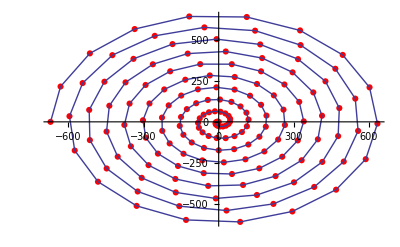

log-scaled discrepancy  sizes

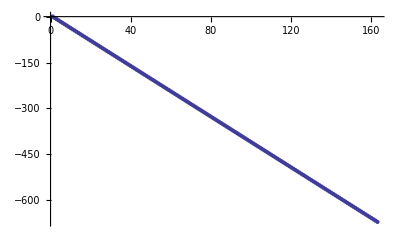

argument changes

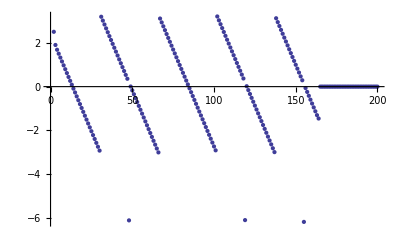

theta  π/3

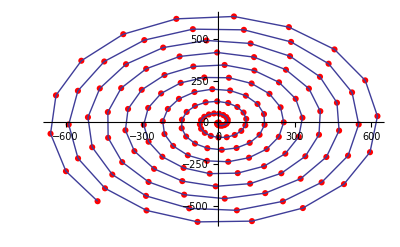

log-scaled discrepancy  sizes

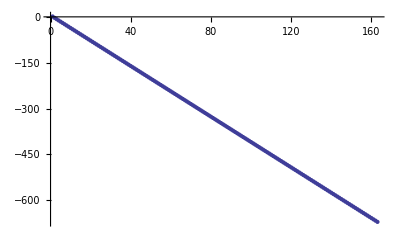

argument changes

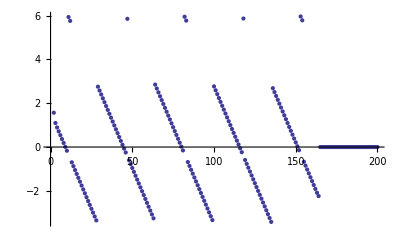

theta  π/2

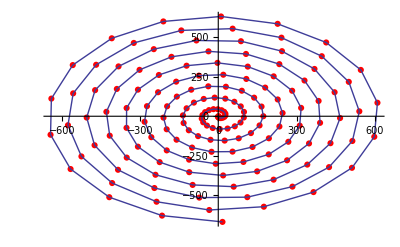

log-scaled discrepancy  sizes

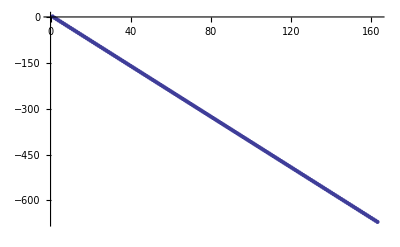

argument changes

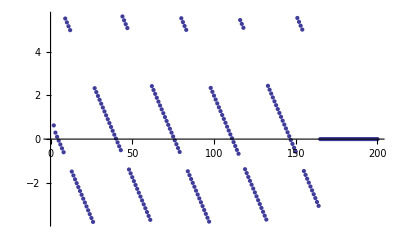

theta  (2 π)/3

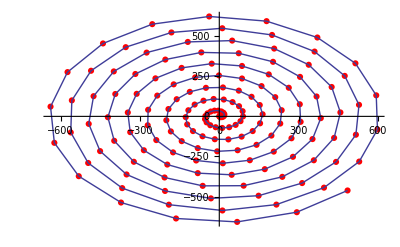

log-scaled discrepancy  sizes

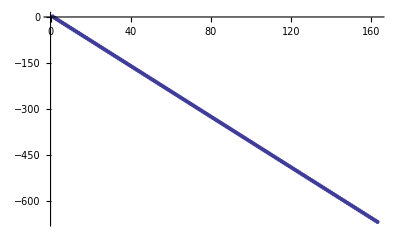

argument changes

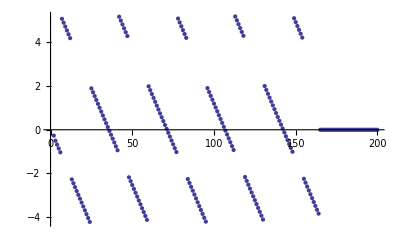

theta  (5 π)/6

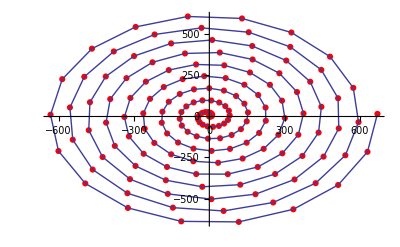

log-scaled discrepancy  sizes

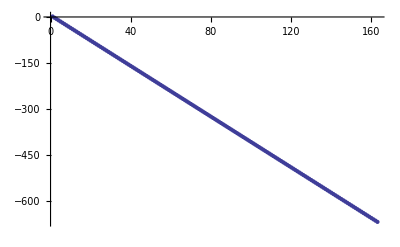

argument changes

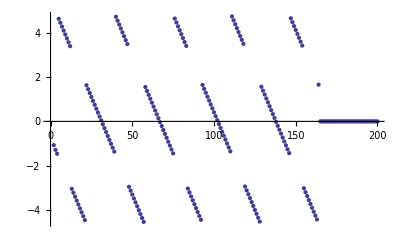

theta  π

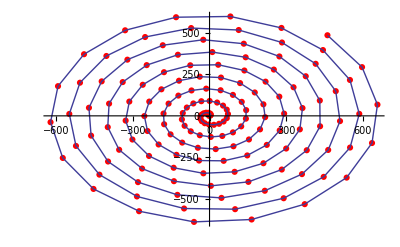

log-scaled discrepancy  sizes

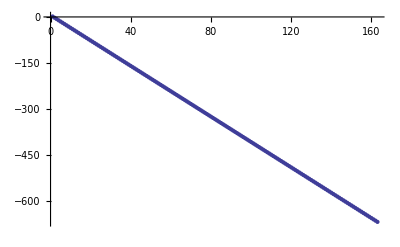

argument changes

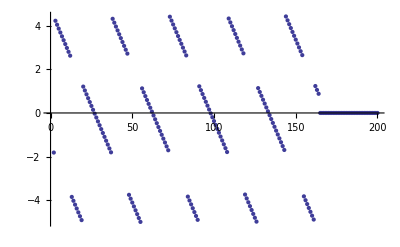

theta  (7 π)/6

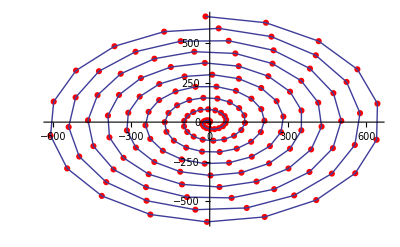

log-scaled discrepancy  sizes

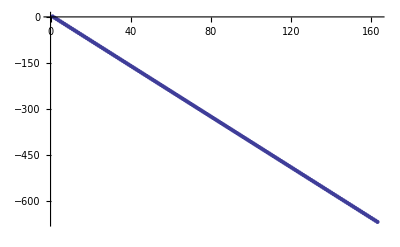

argument changes

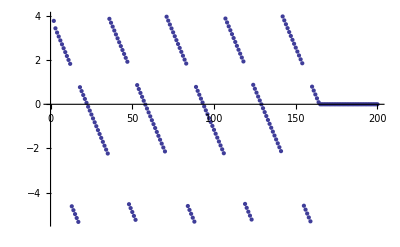

theta  (4 π)/3

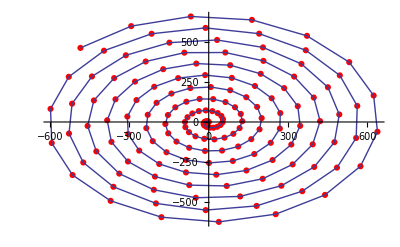

log-scaled discrepancy  sizes

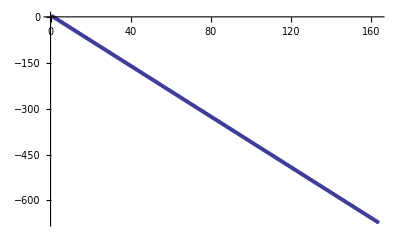

argument changes

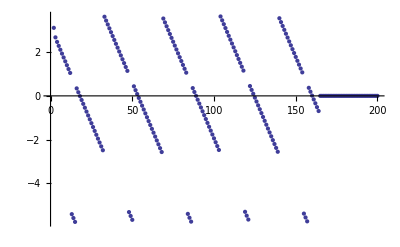

theta  (3 π)/2

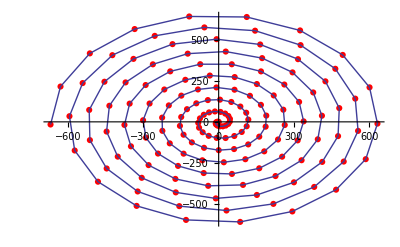

log-scaled discrepancy  sizes

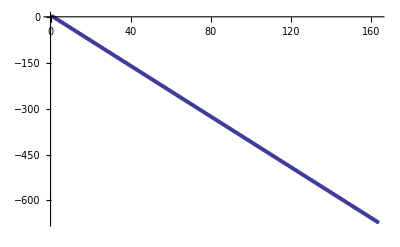

argument changes

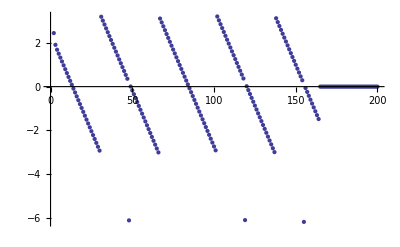

theta  (5 π)/3

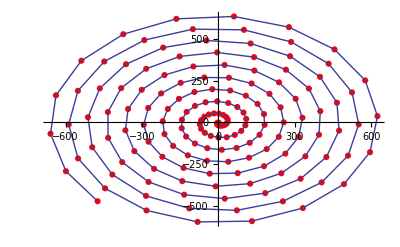

log-scaled discrepancy  sizes

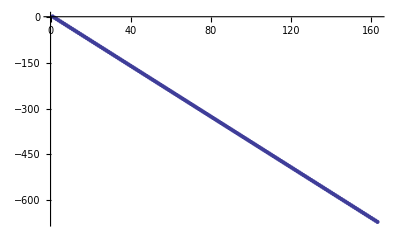

argument changes

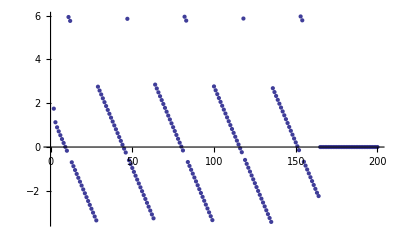

theta  (11 π)/6

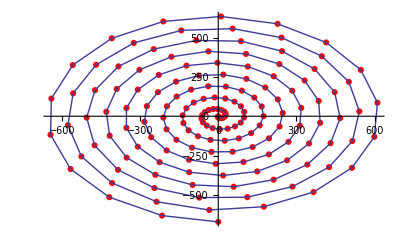

log-scaled discrepancy  sizes

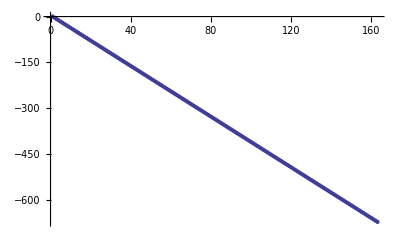

argument changes

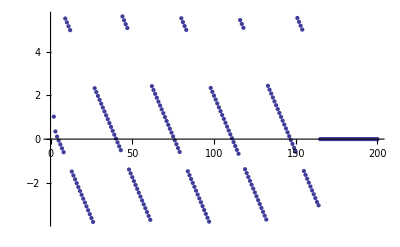

theta  2 π

-Graphics-

log-scaled discrepancy  sizes

-Graphics-

argument changes

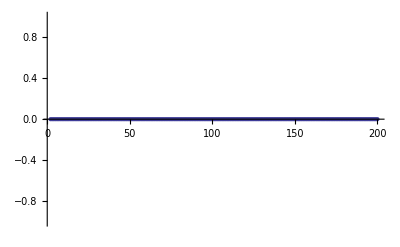

```mathematica
streem=OpenRead["cardioidfx4rho1spiral9mar16no2"];
ls=ReadList[streem];
Close[streem];

For[theta=0,theta<2*Pi,theta=theta+Pi/6;
discrepancies={};
logabsdiscs={};
rels={};
abrels={};
points={};
argdiffs={};
Print["theta  ",theta];
rotate[a_]:=Exp[I*theta]*(a-fxx)+fxx;
For[n=0,n<199,n++;
k=ls[[n,1]];
u=ls[[n,2]];
disc=rotate[Zeta[u]]-Zeta[rotate[u]];
logabsdisc=Re[Log[Abs[disc]]];
discrepancies=Append[discrepancies,disc];
logabsdiscs=Append[logabsdiscs,logabsdisc];
rel=logabdisc/u;
rels=Append[rels,rel];
abrels=Append[abrels,Abs[rel]];
point={Log[Abs[disc]]*Cos[Arg[disc]],Log[Abs[disc]]*Sin[Arg[disc]]};
argdiff=Arg[u-fxx]-Arg[disc];
argdiffs=Append[argdiffs,{k,argdiff}];
points=Append[points,point]];
Print[Show[ListPlot[points,PlotRange->Full,PlotStyle->{Red,PointSize[.0110]}],ListPlot[points,PlotRange->Full,Joined->True]]];
Print["log-scaled discrepancy  sizes"];
Print[ListPlot[logabsdiscs]];
Print["argument changes"];
Print[ListPlot[argdiffs]]

]
```